## Transistor Sizes

```mathematica
Xbk=XA10={6.*10^-7,1.96*10^-6};
Xm=XA1={9.2*10^-7,5.01*10^-6};
XA3=XA4={6.*10^-7,4.12*10^-6};
XA2=XA5=XA6=XA3=XA4={6.*10^-7,1.36*10^-6};
XB2={6.93*10^-7,1.85*10^-6};
XA12={6.5*10^-7,3.3*10^-6};
Xlk=XB1=XB2 =XA1=XA10=XA12=XA7= Xm=Xbk={6.5*10^-7,4.33*10^-6};
TransistorList={XB1,XB2,XA1,XA2,XA3,XA4,XA5,XA6,XA7,XA10,XA12};
```

## Alpha Values

```mathematica
α=#⟦1⟧/#⟦2⟧&;
alphaList=α[#]&/@TransistorList
```

{0.150115,0.150115,0.150115,0.441176,0.441176,0.441176,0.441176,0.441176,0.150115,0.150115,0.150115}

### Width Calculator

```mathematica
WidthCalc[X_,l_]:=α[X]*l;
LengthCalc[X_,w_]:=w/α[X];
```

### Plot of α Values

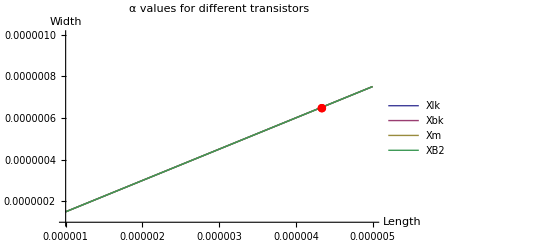

```mathematica
Show[Plot[{WidthCalc[Xlk,l],WidthCalc[Xbk,l],WidthCalc[Xm,l],WidthCalc[XB2,l]},{l,1*10^-6,5*10^-6},PlotRange->{1*10^-7,1*10^-6}, PlotLegends->{"Xlk", "Xbk", "Xm", "XB2"}, AxesLabel->{Length, Width}, PlotLabel->"α values for different transistors"],
ListPlot[{{XB2⟦2⟧,XB2⟦1⟧}},PlotStyle->Red,PlotMarkers->{"●",Medium}]]
```

## Capacitance Extraction from data from SPICE

### Soma's Capacitor

Data comes in the form of a list of {x μs, y V}
Then this script takes this list and gets the slope of the line, and uses that to calculate the capacitor’s value using the equation:
	I=C dV/dt, where dV/dtequals the slope and I is a value input by the user as Iconst

#### Data Input and Massaging

```mathematica
dataSoma={{4,0.72921},{5,0.83853},{6,0.94822},{7,1.0585},{8,1.1691},{9,1.2796},{10,1.3912}};
dataSoma⟦;;,1⟧ = #*1.*10^-6&/@dataSoma⟦;;,1⟧;
lineSoma=Fit[dataSoma,{1,x},x]
```

110321. x+0.286947

#### Plot

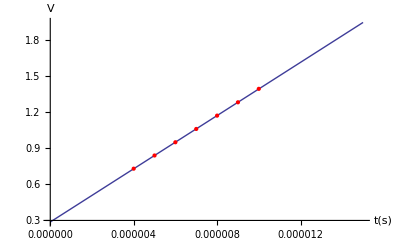

```mathematica
Show[
Plot[{lineSoma},{x,0,15*10^-6},AxesLabel->{"t(s)","V"}],
ListPlot[dataSoma, PlotStyle->Red]
]
```

#### Capacitor Value Calculation

```mathematica
IconstSoma=Quantity[10,"NanoAmps"];
dvdtSoma=Quantity[lineSoma[[2,1]],"Volts/Seconds"];
Cm=UnitConvert[UnitSimplify[IconstSoma/dvdtSoma],"FemtoFarads"];
Row[{"C_m: ", Cm}]
```

C_m: 90.6445

### Capacitance Extraction from data from SPICE (for refractory)

Data comes in the form of a list of {x μs, y V}
Then this script takes this list and gets the slope of the line, and uses that to calculate the capacitor’s value using the equation:
	I=C dV/dt, where dV/dtequals the slope and I is a value input by the user as Iconst

#### Data Input and Massaging

```mathematica
dataRef={{4,1.066},{5,1.2604},{6,1.4571},{7,1.6541},{8,1.8515},{9,2.0516},{10,2.2516},{15,3.2695},{20,4.3123},{25,5.3776},{30,6.4609},{35,7.5519},{40,8.6291},{45,9.6686},{50,10.667}};
dataRef⟦;;,1⟧ = #*1.*10^-6&/@dataRef⟦;;,1⟧;
lineRef=Fit[dataRef⟦1;;7⟧,{1,x},x]
```

197629. x+0.272643

#### Plot

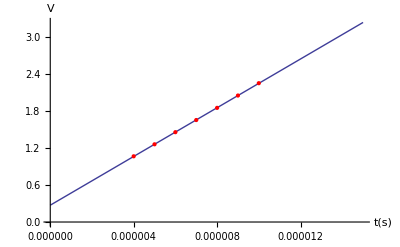

```mathematica
Show[
Plot[{lineRef},{x,0,15*10^-6},AxesLabel->{"t(s)","V"}],
ListPlot[dataRef⟦1;;7⟧, PlotStyle->Red]
]
```

#### Capacitor Value Calculation

```mathematica
IconstRef=Quantity[10,"NanoAmps"];
dvdtRef=Quantity[lineRef[[2,1]],"Volts/Seconds"];
Cref=UnitConvert[UnitSimplify[IconstRef/dvdtRef],"FemtoFarads"];
Row[{"C_ref: ", Cref}]
```

C_ref: 50.6

```mathematica
Ut[25]
```

0.025693

```mathematica
ptau=.;
```

## Calibration Parameters

```mathematica
Vdd=Quantity[1.8, "Volts"];
Ut[T_]:=UnitSimplify[UnitConvert[Quantity[T ,"DegreesCelsius"],"Kelvins"]*Quantity["BoltzmannConstant"] /Quantity["ElementaryCharge"]];
pqua=(2α[XB1]α[XA6]α[XA1]α[XA10])/(α[XA7]^2 α[XB2](α[XA4]+α[XA6]));
ptau[kappa_]:=(α[XB1]*Cm*Ut[25])/(α[XA7] kappa);
pref=(Cref Vdd)/α[XA12];
Ileak[τm_,kappa_]:=UnitConvert[Quantity[ptau[kappa]/Quantity[τm,"Seconds"]],"FemtoAmps"];
Iinput[ιin_,Ilk_]:=UnitConvert[(ιin Ilk)/pqua,"FemtoAmps"];
Iref[tref_]:=UnitConvert[Quantity[pref/Quantity[tref,"Seconds"]],"PicoAmps"];
τCalc[Ilk_,kappa_]:=UnitConvert[Quantity[ptau[kappa]/Quantity[Ilk,"FemtoAmps"]],"Seconds"];
ιinCalc[Iin_,Ilk_]:=pqua Iin/Ilk;
trefCalc[Iref_]:=UnitConvert[Quantity[pref/Quantity[Iref,"PicoAmps"]],"Seconds"];
Manipulate[
Grid[{{
Grid[{{"ρ_qua: ", pqua},{"ρ_tau: ", ptau[κ1]},{"ρ_ref: ",pref}}],
Manipulate[
Grid[{
{"I_input: ", Iinput[ιin,Ileak[τ,κ1]]},
{"I_leak: ",Ileak[τ,κ1]},
{"I_ref: ",Iref[tref]}
}],(*Grid*)
{{ιin,0.51,"i_in"},0,2.0,0.01,Appearance->{"Labeled","Open"}},
{{τ,0.01,"τ_m"},0.001,0.050,0.001,Appearance->{"Labeled","Open"}},
{{tref,0.001,"t_ref"},0.001,0.02,0.001,Appearance->{"Labeled","Open"}}
(*{{κ1,0.6,"κ"},{0.4,0.5,0.6,0.7}}*)
](*Manipulate*),
Manipulate[
Grid[{
{"ι_in: ", ιinCalc[Iin,Ilk]},
{"τ_m: ",τCalc[Ilk,κ1]},
{"t_ref: ",trefCalc[Iref]}
}],(*Grid*)
{{Iin,340,"I_in"},100,10000,10,Appearance->{"Labeled","Open"}},
{{Ilk,475,"I_lk"},100,4000,10,Appearance-> {"Labeled","Open"}},
{{Iref,600,"I_ref"},100,10000,10,Appearance->{"Labeled","Open"}}
(*{{κ1,0.7,"κ"},{0.4,0.5,0.6,0.7}}*)
](*Manipulate*)
}}
],
{{κ1,0.7,"κ"},{0.4,0.5,0.6,0.7}}]
```

## Current Bias Values

```mathematica
Ilk=3.5*10^-9;
Iin=10*10^-9;
Ibk=3.5*10^-9
Isoma=α[Xm]*(α[Xbk]/Ibk)*((Ilk*Iin)/(α[Xlk]*α[XB2]))
```

3.5×10^-9

9.99674×10^-9

## Old/Obsolete

### Calculate Capacitance Value using Time Constant

Vc=Vs(1-E^(-t/(R C)))
Vc/Vs=1-E^(-t/(R C))
E^(-t/(R C))=1-Vc/Vs
-t/(R C)=Log[1-Vc/Vs]

```mathematica
CapVal[Vc_, Vs_,t_, R_]:=-t/(R Log[1-Vc/Vs]);
```

```mathematica
CapVal[ 5.0, 10,55.118*10^-12, 1000]
CapVal[ 9.0, 10,194.51*10^-12, 1000]
CapVal[ 9.9, 10,403.39*10^-12, 1000]
```

7.95185×10^-14

8.44746×10^-14

8.7595×10^-14

```mathematica
CapVal[ 0.5, 1,25.128*10^-12, 1000]
CapVal[0.632, 1,55.167*10^-12, 1000]
CapVal[0.9, 1,183.71*10^-12, 1000]
CapVal[ 0.99, 1,414.12*10^-12, 1000]
```

3.6252×10^-14

5.51851×10^-14

7.97842×10^-14

8.9925×10^-14